# Mass Differences

We’ll use the following mesons\baryons for the analysis. I’ve tabulated mass, possible charges, slope, intercept. They are all of angular momentum 0.

## determination of charge and masses

## Data

```mathematica
(*The mass of the Ksp is the hadroproduced one*)
Mass=<|
(*mesons*)
Kaonp-> 493.6 , Kaon0-> 497.6 , Ksp->891.66,Ksn->  895.81,Dn-> 1864.84,Dp-> 1896.61  ,πp-> 139.57,πn-> 134.97,ρn->775.26,ρp->775.26,Bn-> 5279.58,Bp-> 5279.26,
(*baryons*)
proton -> 938.272,neutron-> 939.5653, Ξcn-> 2470.88,Ξcp-> 2467.8,Λcp->2286.46,Σcp->2452.9,Σcn->2453.74,Σp->1189.3,Σn->1192.6 ,Ξ2n-> 1531.8,Ξ2m-> 1535 , Ξn-> 1315,Ξm->1322|>;
m1=<|Kaon->  ms, proton ->mu ,neutron-> md, Ksp-> ms, Ksn-> ms,Ξcn-> mc,Ξcp-> mc,Λcp->md,Dp->md,Dn->mu,πp-> mu,πn-> (mu+md)/2,Σcp->mc,Σcn->mc,Σp->ms,Σn->ms ,Ξ2n-> ms,Ξ2m-> ms,ρn->(mu+md)/2,ρp->mu,Bn-> mb,Bp-> mb, Ξn-> ms,Ξm->ms|>;
m2=<|Kaon-> md, proton -> md,neutron-> md,Ksp-> mu, Ksn-> md,Ξcn-> md,Ξcp-> mu,Λcp->mc,Dp->mc,Dn->mc,πp-> md,πn-> (mu+md)/2,Σcp->mu,Σcn->md,Σp->mu,Σn->md,Ξ2n-> mu,Ξ2m-> md,ρn->(mu+md)/2,ρp->md,Bn-> md,Bp-> mu, Ξn->mu,Ξm->md|>;
α=<|
(*mesons*)
Dp->1.073,Dn->1.073,πp->0.83,πn->0.83 ,ρn->0.896,ρp->0.896,Kaon->  0.8875,Bn-> 0.204,Bp-> 0.204,Ksp-> 0.927,Ksn->0.927, 
(*baryons*)
proton-> 0.944,neutron-> 0.944,Ξcn-> 0.95,Ξcp-> 0.95,Λcp->0.95,(*Σcn->,Σcp->,*)Σn->0.95,Σp->0.95,Ξ2n->0.95,Ξ2m->0.95, Ξn->.95,Ξm-> .95 |>;
a=<|
(*mesons*)
Dp->-0.07,Dn->-0.07,πp->-0.23,πn->-0.23,Kaon->  0.57,Ksp-> 0.32,Ksn-> 0.32,ρn->0.52,ρp->0.52,Bn-> -5.7,Bp-> -5.7,
(*baryons*)
 proton ->-0.32,neutron ->-0.32,Ξcn-> -0.13,Ξcp-> -0.13,Λcp->-0.68 ,(*Σcn->,Σcp->,*)Σn->0.27,Σp->0.27,Ξ2n->-0.04 ,Ξ2m->-0.04, Ξn->-0.04,Ξm-> -0.04|>;
Spin=<|Kaon-> 0,Ksp-> 1,Ksn-> 1, proton ->1/2,neutron ->1/2 ,Ξcn-> 1/2,Ξcp-> 1/2,Λcp->1/2,Dn-> 0,Dp-> 0,πp->0,πn->0,Σcp->1/2,Σcn->1/2,Σp->1/2,Σn->1/2,Ξ2n->3/2 ,Ξ2m->3/2,ρn->1,ρp->1,Bn-> 0,Bp-> 0, Ξn->1/2,Ξm-> 1/2|>;
Q=<|Kaon->  0.57,Ksp->2/9,Ksn->-1/9 , proton -> 2/9,neutron-> -1/9,Ξcn-> -1/9,Ξcp-> 2/9,Λcp->2/9,Dn-> -4/9,Dp-> 2/9,πp->2/9,πn->-5/18,Σcp->2/9,Σcn->-1/9,Σp->2/9,Σn->-1/9,Ξ2n->-4/9 ,Ξ2m->2/9,ρn->-5/18,ρp->2/9,Bn-> -1/9,Bp->2/9, Ξn->-4/9,Ξm-> 2/9 |>;
```

## Calculation

The energy not due to end points is actually (now letting the charge be arbitrary)

```mathematica
L[key_,csq_]:=π √(10^-6 α[key])(√(Spin[key]-a[key])+√(Spin[key]-a[key]+csq(8 Q[key])/π));
M[key_,csq_]:= 1/(2π 10^-6 α[key])L[key,csq]+csq Q[key]/L[key,csq](*+√((Spin[key]-a[key])/(10^-6 α[key]))*);
TotM[key_,csq_]:=M[key,csq]+m1[key]+m2[key];
```

Now plot the energy differences due to charge and string tension, minus the difference in the actual experimental mass. This should give the mass difference in the end points needed to explain the mass difference.

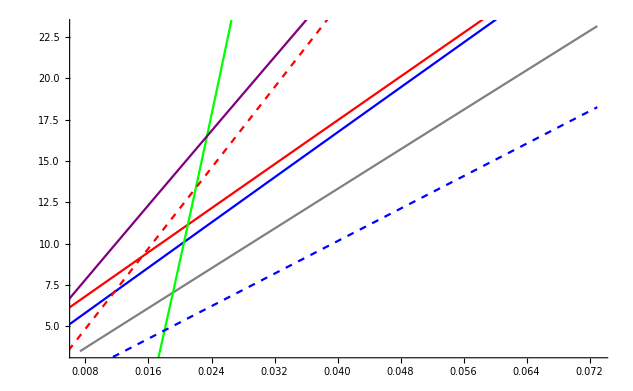

```mathematica
Nbaryon=Plot[Mass[neutron]-Mass[proton
]-M[neutron,csq]+M[proton,csq],{csq,1/137,10/137},PlotStyle->Gray];
Ks=Plot[Mass[Ksn]-Mass[Ksp]-M[Ksn,csq]+M[Ksp,csq],{csq,0.5/137,10/137},PlotStyle->Red];
Ξc=Plot[Mass[Ξcn]-Mass[Ξcp]-M[Ξcn,csq]+M[Ξcp,csq],{csq,0.5/137,10/137},PlotStyle->Blue];
Dmes=Plot[Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,0.5/137,10/137},PlotStyle->Green];
(*Σc=Plot[Mass[Σcn]-Mass[Σcp]-M[Σcn,csq]+M[Σcp,csq],{csq,0.5/137,10/137},PlotStyle->Yellow];*)
Σ=Plot[Mass[Σn]-Mass[Σp]-M[Σn,csq]+M[Σp,csq],{csq,0.5/137,10/137},PlotStyle->Purple];
ρ=Plot[Mass[ρn]-Mass[ρp]-M[ρn,csq]+M[ρp,csq],{csq,0.5/137,10/137},PlotStyle->{Dashed,Red}];
B=Plot[Mass[Bn]-Mass[Bp]-M[Bn,csq]+M[Bp,csq],{csq,0.5/137,10/137},PlotStyle->{Dashed,Blue}];
Show[Nbaryon,Ks,Ξc,Dmes(*,Σc*),Σ,ρ,B]
```

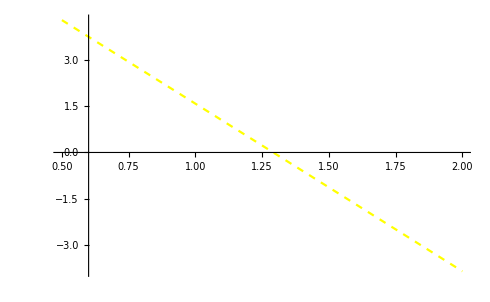

```mathematica
Ξ=Plot[Mass[Ξm]-Mass[Ξn]-M[Ξm,csq/137]+M[Ξn,csq/137],{csq,0.5,2},PlotStyle->{Dashed,Yellow}];
Show[Ξ]
```

```mathematica
Mass[Ξm]-Mass[Ξn]-M[Ξm,1/137]+M[Ξn,1/137]
```

1.583

```mathematica
N[1/137]
```

0.00729927

There is an intersection
For the N baryon the mass difference is md-mu
For the K^* the mass difference is md-mu
For the Ξ_c the mass difference is md-mu
For the D the mass difference is md-mu
For the Σ_c the mass difference is md-mu
For the Σ the mass difference is md-mu
We can thus get very good agreement on the mass difference (The K^* should get a seperate treatment. Also this could be due to peculiarities in the mass of the K^*...) of d and u quarks.

```mathematica
FindRoot[Mass[neutron]-Mass[proton]-M[neutron,csq]+M[proton,csq]==Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,1/137}]
(Mass[neutron]-Mass[proton]-M[neutron,csq]+M[proton,csq]) /.FindRoot[Mass[Ξcn]-Mass[Ξcp]-M[Ξcn,csq]+M[Ξcp,csq]==Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,1/137}]
```

{csq→0.0491407}

7.36312

This Gives a charge squared of about

```mathematica
N[6.5/137]
```

0.0474453

We can now fix the charge squared to this value and calculate the masses of the up and down quarks from the equations for the proton and neutron

```mathematica
CSQ=csq/.FindRoot[Mass[neutron]-Mass[proton]-M[neutron,csq]+M[proton,csq]==Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,1/137}];
mdmuSol=NSolve[{TotM[neutron,CSQ]== Mass[neutron],TotM[proton,CSQ]== Mass[proton]},{md,mu}]
```

{{md→17.7615,mu→10.3792}}

A consistency check is the mass of the pion, which turns out as

```mathematica
TotM[πp,CSQ]
Mass[πp]
```

391.094+md+mu

139.57

which is inconsistent. This tells us our model is not fit to determine the π mass as is.
Knowing these masses now enables us to determine the mass of the charm quark through the Ξ_c,Σ_c baryons and D Meson, and also consistency checks at the same time (the system of equations is over determined)

```mathematica
NSolve[TotM[Ξcn,CSQ]== Mass[Ξcn],{mc}]/.mdmuSol
NSolve[TotM[Ξcp,CSQ]== Mass[Ξcp],{mc}]/.mdmuSol
```

{{{mc→1144.63}}}

{{{mc→1144.75}}}

```mathematica
NSolve[TotM[Dn,CSQ]== Mass[Dn],{mc}]/.mdmuSol
NSolve[TotM[Dp,CSQ]== Mass[Dp],{mc}]/.mdmuSol
```

{{{mc→1625.81}}}

{{{mc→1611.05}}}

```mathematica
NSolve[TotM[Σcn,CSQ]== Mass[Σcn],{mc}]/.mdmuSol
NSolve[TotM[Σcp,CSQ]== Mass[Σcp],{mc}]/.mdmuSol
```

{{{mc→1604.67}}}

{{{mc→1604.63}}}

We can now use the Σ baryons as a probe into the strange quark.

```mathematica
NSolve[TotM[Σn,CSQ]== Mass[Σn],{ms}]/.mdmuSol
NSolve[TotM[Σp,CSQ]== Mass[Σp],{ms}]/.mdmuSol
```

{{{ms→343.528}}}

{{{ms→341.034}}}

TODO
units of charge-Jackson,try universal fit values,more?

## universal fit feasibility

## Data

```mathematica
(*The mass of the Ksp is the hadroproduced one*)
Mass=<|Kaonp-> 493.6 , Kaon0-> 497.6 , proton -> 938.272,neutron-> 939.5653,Ksp->891.66,Ksn->  895.81, Ξcn-> 2470.88,Ξcp-> 2467.8,Λcp->2286.46,Dn-> 1864.84,Dp-> 1896.61  ,πp-> 139.57,πn-> 134.97,Σcp->2452.9,Σcn->2453.74,Σp->1189.3,Σn->1192.6 ,Ξ2n-> 1531.8,Ξ2m-> 1535,ρn->775.26,ρp->775.26,Bn-> 5279.58,Bp-> 5279.26 , Ξn-> 1315,Ξm->1322|>;
m1=<|Kaon->  ms, proton ->mu ,neutron-> md, Ksp-> ms, Ksn-> ms,Ξcn-> mc,Ξcp-> mc,Λcp->md,Dp->md,Dn->mu,πp-> mu,πn-> (mu+md)/2,Σcp->mc,Σcn->mc,Σp->ms,Σn->ms ,Ξ2n-> ms,Ξ2m-> ms,ρn->(mu+md)/2,ρp->mu,Bn-> mb,Bp-> mb, Ξn-> ms,Ξm->ms|>;
m2=<|Kaon-> md, proton -> md,neutron-> md,Ksp-> mu, Ksn-> md,Ξcn-> md,Ξcp-> mu,Λcp->mc,Dp->mc,Dn->mc,πp-> md,πn-> (mu+md)/2,Σcp->mu,Σcn->md,Σp->mu,Σn->md,Ξ2n-> ms,Ξ2m-> ms,ρn->(mu+md)/2,ρp->md,Bn-> md,Bp-> mu, Ξn->ms,Ξm->ms|>;
Spin=<|Kaon-> 0,Ksp-> 1,Ksn-> 1, proton ->1/2,neutron ->1/2 ,Ξcn-> 1/2,Ξcp-> 1/2,Λcp->1/2,Dn-> 0,Dp-> 0,πp->0,πn->0,Σcp->1/2,Σcn->1/2,Σp->1/2,Σn->1/2,Ξ2n->3/2 ,Ξ2m->3/2,ρn->1,ρp->1,Bn-> 0,Bp-> 0, Ξn->1/2,Ξm-> 1/2|>;
Q=<|Kaon->  0.57,Ksp->2/9,Ksn->-1/9 , proton -> 2/9,neutron-> -1/9,Ξcn-> -1/9,Ξcp-> 2/9,Λcp->2/9,Dn-> -4/9,Dp-> 2/9,πp->2/9,πn->-5/18,Σcp->2/9,Σcn->-1/9,Σp->2/9,Σn->-1/9,Ξ2n->-1/9 ,Ξ2m->2/9,ρn->-5/18,ρp->2/9,Bn-> -1/9,Bp->2/9 , Ξn->-1/9,Ξm-> 2/9|>;
α=<|Ksp->0.884,Ksn->0.884, proton-> 0.949,neutron-> 0.949,Ξcn->0.95,Ξcp-> 0.95,Λcp->0.95,Dp->0.884,Dn->0.884,πp->0.884,πn->0.884 ,Σcn->0.95,Σcp->0.95,Σn->0.95,Σp->0.95,Ξ2n->0.95,Ξ2m->0.95 ,ρn->0.884,ρp->0.884,Bn-> 0.884,Bp-> 0.884, Ξn->.95,Ξm-> .95|>;
a=<|Ksp-> 0.5,Ksn-> 0.5, proton ->-0.32,neutron ->-0.32,Ξcn-> -0.13,Ξcp-> -0.13,Λcp->-0.36 ,Dp->-0.19,Dn->-0.19,πp->-0.12,πn->-0.12(*,Σcn->,Σcp->*),Σn->0.27,Σp->0.27,Ξ2n->-0.04 ,Ξ2m->-0.04,ρn->0.52,ρp->0.52,Bn-> -5.7,Bp-> -5.7, Ξn->-0.04,Ξm-> -0.04|>;
```

## Calculation

The energy not due to end points is actually (now letting the charge be arbitrary)

```mathematica
L[key_,csq_]:=π √(10^-6 α[key])(√(Spin[key]-a[key])+√(Spin[key]-a[key]+csq(8 Q[key])/π));
M[key_,csq_]:= 1/(2π 10^-6 α[key])L[key,csq]+csq Q[key]/L[key,csq](*+√((Spin[key]-a[key])/(10^-6 α[key]))*);
TotM[key_,csq_]:=M[key,csq]+m1[key]+m2[key];
```

Now plot the energy differences due to charge and string tension, minus the difference in the actual experimental mass. This should give the mass difference in the end points needed to explain the mass difference.

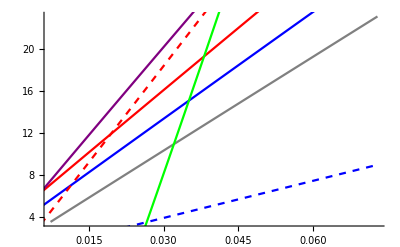

```mathematica
Nbaryon=Plot[Mass[neutron]-Mass[proton]-M[neutron,csq]+M[proton,csq],{csq,1/137,10/137},PlotStyle->Gray];
Ks=Plot[Mass[Ksn]-Mass[Ksp]-M[Ksn,csq]+M[Ksp,csq],{csq,0.5/137,10/137},PlotStyle->Red];
Ξc=Plot[Mass[Ξcn]-Mass[Ξcp]-M[Ξcn,csq]+M[Ξcp,csq],{csq,0.5/137,10/137},PlotStyle->Blue];
Dmes=Plot[Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,0.5/137,10/137},PlotStyle->Green];
(*Σc=Plot[Mass[Σcn]-Mass[Σcp]-M[Σcn,csq]+M[Σcp,csq],{csq,0.5/137,10/137},PlotStyle->Yellow];*)
Σ=Plot[Mass[Σn]-Mass[Σp]-M[Σn,csq]+M[Σp,csq],{csq,0.5/137,10/137},PlotStyle->Purple];
Ξ2=Plot[Mass[Ξ2m]-Mass[Ξ2n]-M[Ξ2m,csq]+M[Ξ2n,csq],{csq,0.5/137,10/137},PlotStyle->Dashed];
ρ=Plot[Mass[ρn]-Mass[ρp]-M[ρn,csq]+M[ρp,csq],{csq,0.5/137,10/137},PlotStyle->{Dashed,Red}];
B=Plot[Mass[Bn]-Mass[Bp]-M[Bn,csq]+M[Bp,csq],{csq,0.5/137,10/137},PlotStyle->{Dashed,Blue}];
Show[Nbaryon,Ks,Ξc,Dmes,(*Σc,*)Σ,ρ,Ξ2,B]
```

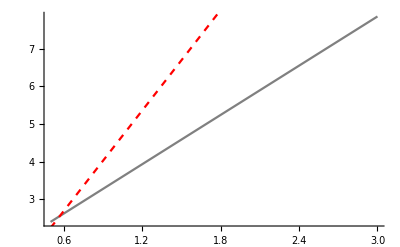

```mathematica
Nbaryon=Plot[Mass[neutron]-Mass[proton]-M[neutron,csq/137]+M[proton,csq/137],{csq,0.5,3},PlotStyle->Gray];
ρ=Plot[Mass[ρn]-Mass[ρp]-M[ρn,csq/137]+M[ρp,csq/137],{csq,0.5,3},PlotStyle->{Dashed,Red}];
Show[Nbaryon,ρ]
```

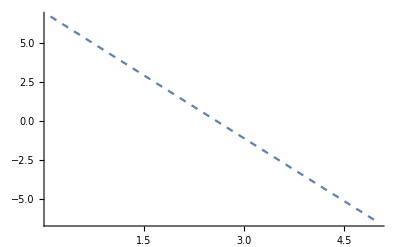

```mathematica
(*Ks=Plot[Mass[Ksn]-Mass[Ksp]-M[Ksn,csq/137]+M[Ksp,csq/137],{csq,0.1,1},PlotStyle->Red];*)
Ξ=Plot[Mass[Ξm]-Mass[Ξn]-M[Ξm,csq/137]+M[Ξn,csq/137],{csq,0.1,5},PlotStyle->Dashed]
(*Show[Ks,Ξ]*)
```

```mathematica
Mass[neutron]-Mass[proton]-M[neutron,3/137]+M[proton,3/137]
```

7.8656

```mathematica
Mass[ρn]-Mass[ρp]-M[ρn,1/137]+M[ρp,1/137]
```

4.46099

```mathematica
Mass[Ξm]-Mass[Ξn]-M[Ξm,2.8/137]+M[Ξn,2.8/137]
```

-0.549217

```mathematica
Mass[Ksn]-Mass[Ksp]-M[Ksn,1/137]+M[Ksp,1/137]
```

7.05932

```mathematica
N[1/137]
```

0.00729927

There is an intersection
For the N baryon the mass difference is md-mu
For the K^* the mass difference is md-mu
For the Ξ_c the mass difference is md-mu
For the D the mass difference is md-mu
For the Σ_c the mass difference is md-mu
For the Σ the mass difference is md-mu
We can thus get very good agreement on the mass difference (The K^* should get a seperate treatment. Also this could be due to peculiarities in the mass of the K^*...) of d and u quarks.

```mathematica
FindRoot[Mass[neutron]-Mass[proton]-M[neutron,csq]+M[proton,csq]==Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,1/137}]
(Mass[neutron]-Mass[proton]-M[neutron,csq]+M[proton,csq]) /.FindRoot[Mass[Ξcn]-Mass[Ξcp]-M[Ξcn,csq]+M[Ξcp,csq]==Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,1/137}]
```

{csq→0.0491407}

7.36312

This Gives a charge squared of about

```mathematica
N[6.5/137]
```

0.0474453

We can now fix the charge squared to this value and calculate the masses of the up and down quarks from the equations for the proton and neutron

```mathematica
CSQ=csq/.FindRoot[Mass[neutron]-Mass[proton]-M[neutron,csq]+M[proton,csq]==Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,1/137}];
mdmuSol=NSolve[{TotM[neutron,CSQ]== Mass[neutron],TotM[proton,CSQ]== Mass[proton]},{md,mu}]
```

{{md→17.7615,mu→10.3792}}

A consistency check is the mass of the pion, which turns out as

```mathematica
TotM[πp,CSQ]
Mass[πp]
```

391.094+md+mu

139.57

which is inconsistent. This tells us our model is not fit to determine the π mass as is.
Knowing these masses now enables us to determine the mass of the charm quark through the Ξ_c,Σ_c baryons and D Meson, and also consistency checks at the same time (the system of equations is over determined)

```mathematica
NSolve[TotM[Ξcn,CSQ]== Mass[Ξcn],{mc}]/.mdmuSol
NSolve[TotM[Ξcp,CSQ]== Mass[Ξcp],{mc}]/.mdmuSol
```

{{{mc→1144.63}}}

{{{mc→1144.75}}}

```mathematica
NSolve[TotM[Dn,CSQ]== Mass[Dn],{mc}]/.mdmuSol
NSolve[TotM[Dp,CSQ]== Mass[Dp],{mc}]/.mdmuSol
```

{{{mc→1625.81}}}

{{{mc→1611.05}}}

```mathematica
NSolve[TotM[Σcn,CSQ]== Mass[Σcn],{mc}]/.mdmuSol
NSolve[TotM[Σcp,CSQ]== Mass[Σcp],{mc}]/.mdmuSol
```

{{{mc→1604.67}}}

{{{mc→1604.63}}}

We can now use the Σ baryons as a probe into the strange quark.

```mathematica
NSolve[TotM[Σn,CSQ]== Mass[Σn],{ms}]/.mdmuSol
NSolve[TotM[Σp,CSQ]== Mass[Σp],{ms}]/.mdmuSol
```

{{{ms→343.528}}}

{{{ms→341.034}}}

TODO
units of charge-Jackson,try universal fit values,more?

## finding the range of parameters

We handle only the particles of endpoint mass difference md-mu and plot the areas where the curves can be (using the allowed range of α and a)

## Data

```mathematica
(*The mass of the Ksp is the hadroproduced one*)
Mass=<|Kaonp-> 493.6 , Kaon0-> 497.6 , proton -> 938.272,neutron-> 939.5653,Ksp->891.66,Ksn->  895.81, Ξcn-> 2470.88,Ξcp-> 2467.8,Dn-> 1864.84,Dp-> 1896.61  ,πp-> 139.57,πn-> 134.97,Σp->1189.3,Σn->1192.6 ,Bn-> 5279.58,Bp-> 5279.26 |>;
m1=<|Kaon->  ms, proton ->mu ,neutron-> md, Ksp-> ms, Ksn-> ms,Ξcn-> mc,Ξcp-> mc,Dp->md,Dn->mu,Σp->ms,Σn->ms ,Bn-> mb,Bp-> mb|>;
m2=<|Kaon-> md, proton -> md,neutron-> md,Ksp-> mu, Ksn-> md,Ξcn-> md,Ξcp-> mu,Dp->mc,Dn->mc,Σp->mu,Σn->md,Bn-> md,Bp-> mu|>;
Spin=<|Kaon-> 0,Ksp-> 1,Ksn-> 1, proton ->1/2,neutron ->1/2 ,Ξcn-> 1/2,Ξcp-> 1/2,Dn-> 0,Dp-> 0,Σp->1/2,Σn->1/2,Ξ2n->3/2 ,Ξ2m->3/2,Bn-> 0,Bp-> 0|>;
Q=<|Kaon->  0.57,Ksp->2/9,Ksn->-1/9 , proton -> 2/9,neutron-> -1/9,Ξcn-> -1/9,Ξcp-> 2/9,Dn-> -4/9,Dp-> 2/9,Σp->2/9,Σn->-1/9,Bn-> -1/9,Bp->2/9 |>;
α=<|Ksp->{0.848,0.927},Ksn->{0.848,0.927}, proton-> {0.949,1.018},neutron->{0.949,1.018},Ξcn->{0.95,0.547},Ξcp->{0.95,0.547},Dp->{0.884,1.073},Dn->{0.884,1.073} ,Σn->{0.95,1.502},Σp->{0.95,1.502},Bn-> 0.884,Bp-> 0.884|>;
a=<|Ksp-> {0.32,0.62},Ksn->{0.32,0.62}, proton ->{-0.32,0.45},neutron ->{-0.32,0.45},Dp->{-0.19,-0.07},Dn->{-0.19,-0.07},Σn->{0.27,1.37},Σp->{0.27,1.37},Bn-> -5.7,Bp-> -5.7,Ξcn->{-0.13,-2.83},Ξcp->{-0.13,-2.83}|>;
```

## Calculation

The energy not due to end points is actually (now letting the charge be arbitrary)

```mathematica
L[key_,csq_,n_]:=π √(10^-6 α[key][[n]])(√(Spin[key]-a[key][[n]])+√(Spin[key]-a[key][[n]]+csq(8 Q[key])/π));
M[key_,csq_,n_]:= 1/(2π 10^-6 α[key][[n]])L[key,csq,n]+csq Q[key]/L[key,csq,n](*+√((Spin[key]-a[key])/(10^-6 α[key]))*);
TotM[key_,csq_,n_]:=M[key,csq,n]+m1[key]+m2[key];
ImplicitΔm[key1_,key2_,csq_,n_]:=Mass[key1]-Mass[key2]-M[key1,csq,n]+M[key2,csq,n]
```

Now plot the energy differences due to charge and string tension, minus the difference in the actual experimental mass. This should give the mass difference in the end points needed to explain the mass difference.

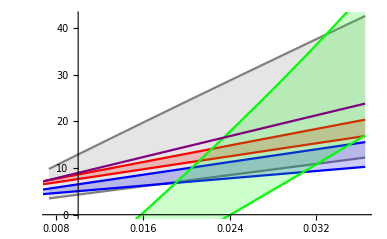

```mathematica
Nbaryon=Plot[{ImplicitΔm[neutron,proton,csq,1],ImplicitΔm[neutron,proton,csq,2]},{csq,1/137,5/137},PlotStyle->Gray,Filling->{1-> {2}}];
Ks=Plot[{ImplicitΔm[Ksn,Ksp,csq,1],ImplicitΔm[Ksn,Ksp,csq,2]},{csq,0.5/137,5/137},PlotStyle->Red,Filling->{1-> {2}}];
Ξc=Plot[{ImplicitΔm[Ξcn,Ξcp,csq,1],ImplicitΔm[Ξcn,Ξcp,csq,2]},{csq,0.5/137,5/137},PlotStyle->Blue,Filling->{1-> {2}}];
Dmes=Plot[{ImplicitΔm[Dn,Dp,csq,1],ImplicitΔm[Dn,Dp,csq,2]},{csq,0.5/137,5/137},PlotStyle->Green,Filling->{1-> {2}}];
Σ=Plot[{ImplicitΔm[Σn,Σp,csq,1],ImplicitΔm[Σn,Σp,csq,2]},{csq,0.5/137,5/137},PlotStyle->Purple,Filling->{1-> {2}}];
Ξ2=Plot[{ImplicitΔm[Ξ2m,Ξ2n,csq,1],ImplicitΔm[Ξ2m,Ξ2n,csq,2]},{csq,0.5/137,5/137},PlotStyle->Dashed,Filling->{1-> {2}}];
ρ=Plot[{ImplicitΔm[ρn,ρp,csq,1],ImplicitΔm[ρn,ρp,csq,2]},{csq,0.5/137,5/137},PlotStyle->{Dashed,Red},Filling->{1-> {2}}];
B=Plot[{ImplicitΔm[Bn,Bp,csq,0],ImplicitΔm[Bn,Bp,csq,0]},{csq,0.5/137,5/137},PlotStyle->{Dashed,Yellow},Filling->{1-> {2}}];
Show[Nbaryon,Ks,Ξc,Dmes,Σ,ρ,Ξ2,B]
```

```mathematica
ImplicitΔm[neutron,proton,0.5,1]
```

175.659

## Result summary

universal

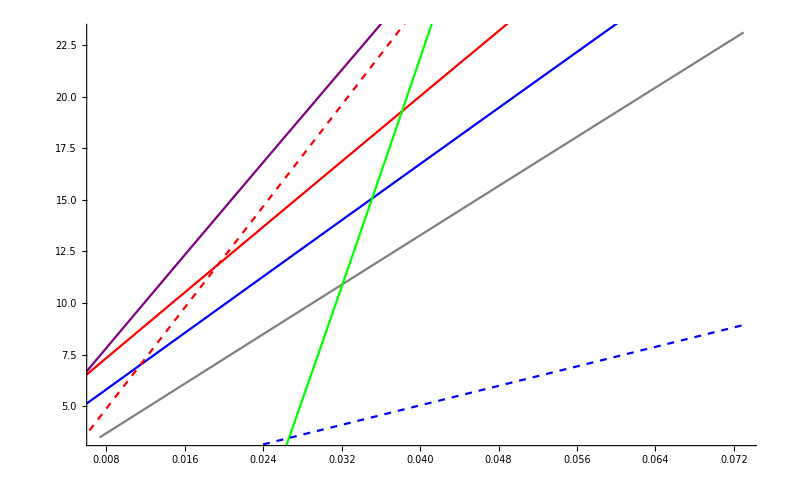

not universal

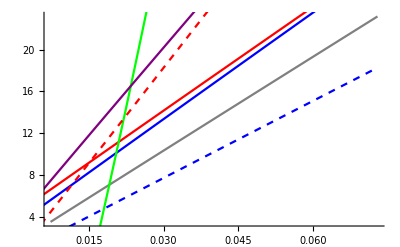

Areas

-Graphics-

Nbaryon -> Gray
Ks -> Red
Ξc -> Blue
Dmes -> Green
Σ -> Purple
Ξj=3/2 -> Dashed
ρ -> {Dashed, Red}
B -> {Dashed, Blue}

TODO
units of charge-Jackson,try universal fit values,more?

## universal fit new intercept effect

## Data

```mathematica
(*The mass of the Ksp is the hadroproduced one*)
Mass=<|Kaonp-> 493.6 , Kaon0-> 497.6 , proton -> 938.272,neutron-> 939.5653,Ksp->891.66,Ksn->  895.81, Ξcn-> 2470.88,Ξcp-> 2467.8,Λcp->2286.46,Dn-> 1864.84,Dp-> 1896.61  ,πp-> 139.57,πn-> 134.97,Σcp->2452.9,Σcn->2453.74,Σp->1189.3,Σn->1192.6 ,Ξ2n-> 1531.8,Ξ2m-> 1535,ρn->775.26,ρp->775.26,Bn-> 5279.58,Bp-> 5279.26 |>;
m1=<|Kaon->  ms, proton ->mu ,neutron-> md, Ksp-> ms, Ksn-> ms,Ξcn-> mc,Ξcp-> mc,Λcp->md,Dp->md,Dn->mu,πp-> mu,πn-> (mu+md)/2,Σcp->mc,Σcn->mc,Σp->ms,Σn->ms ,Ξ2n-> ms,Ξ2m-> ms,ρn->(mu+md)/2,ρp->mu,Bn-> mb,Bp-> mb|>;
m2=<|Kaon-> md, proton -> md,neutron-> md,Ksp-> mu, Ksn-> md,Ξcn-> md,Ξcp-> mu,Λcp->mc,Dp->mc,Dn->mc,πp-> md,πn-> (mu+md)/2,Σcp->mu,Σcn->md,Σp->mu,Σn->md,Ξ2n-> ms,Ξ2m-> ms,ρn->(mu+md)/2,ρp->md,Bn-> md,Bp-> mu|>;
Spin=<|Kaon-> 0,Ksp-> 1,Ksn-> 1, proton ->1/2,neutron ->1/2 ,Ξcn-> 1/2,Ξcp-> 1/2,Λcp->1/2,Dn-> 0,Dp-> 0,πp->0,πn->0,Σcp->1/2,Σcn->1/2,Σp->1/2,Σn->1/2,Ξ2n->3/2 ,Ξ2m->3/2,ρn->1,ρp->1,Bn-> 0,Bp-> 0|>;
Q=<|Kaon->  0.57,Ksp->2/9,Ksn->-1/9 , proton -> 2/9,neutron-> -1/9,Ξcn-> -1/9,Ξcp-> 2/9,Λcp->2/9,Dn-> -4/9,Dp-> 2/9,πp->2/9,πn->-5/18,Σcp->2/9,Σcn->-1/9,Σp->2/9,Σn->-1/9,Ξ2n->-1/9 ,Ξ2m->2/9,ρn->-5/18,ρp->2/9,Bn-> -1/9,Bp->2/9 |>;
α=<|Ksp->0.884,Ksn->0.884, proton-> 0.949,neutron-> 0.949,Ξcn->0.95,Ξcp-> 0.95,Λcp->0.95,Dp->0.884,Dn->0.884,πp->0.884,πn->0.884 ,Σcn->0.95,Σcp->0.95,Σn->0.95,Σp->0.95,Ξ2n->0.95,Ξ2m->0.95 ,ρn->0.884,ρp->0.884,Bn-> 0.884,Bp-> 0.884|>;
a=<|Ksp-> 0.5,Ksn-> 0.5, proton ->-0.32,neutron ->-0.32,Ξcn-> -0.13,Ξcp-> -0.13,Λcp->-0.36 ,Dp->-0.19,Dn->-0.19,πp->-0.12,πn->-0.12(*,Σcn->,Σcp->*),Σn->0.27,Σp->0.27,Ξ2n->-0.04 ,Ξ2m->-0.04,ρn->0.52,ρp->0.52,Bn-> -5.7,Bp-> -5.7|>;
```

## Calculation

The energy not due to end points is actually (now letting the charge be arbitrary)

```mathematica
L[key_,csq_]:=√(2π)√((csq Q[key]-a[key])/(α[key] 10^-6));
M[key_,csq_]:= 1/(2π 10^-6 α[key])L[key,csq]+(csq Q[key]-a[key])/L[key,csq](*+√((Spin[key]-a[key])/(10^-6 α[key]))*);
TotM[key_,csq_]:=M[key,csq]+m1[key]+m2[key];
```

Now plot the energy differences due to charge and string tension, minus the difference in the actual experimental mass. This should give the mass difference in the end points needed to explain the mass difference.

```mathematica
Nbaryon=Plot[Mass[neutron]-Mass[proton
]-M[neutron,csq]+M[proton,csq],{csq,1/137,10/137},PlotStyle->Gray];
Ks=Plot[Mass[Ksn]-Mass[Ksp]-M[Ksn,csq]+M[Ksp,csq],{csq,0.5/137,10/137},PlotStyle->Red];
Ξc=Plot[Mass[Ξcn]-Mass[Ξcp]-M[Ξcn,csq]+M[Ξcp,csq],{csq,0.5/137,10/137},PlotStyle->Blue];
Dmes=Plot[Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,0.5/137,10/137},PlotStyle->Green];
(*Σc=Plot[Mass[Σcn]-Mass[Σcp]-M[Σcn,csq]+M[Σcp,csq],{csq,0.5/137,10/137},PlotStyle->Yellow];*)
Σ=Plot[Mass[Σn]-Mass[Σp]-M[Σn,csq]+M[Σp,csq],{csq,0.5/137,10/137},PlotStyle->Purple];
Ξ2=Plot[Mass[Ξ2m]-Mass[Ξ2n]-M[Ξ2m,csq]+M[Ξ2n,csq],{csq,0.5/137,10/137},PlotStyle->Dashed];
ρ=Plot[Mass[ρn]-Mass[ρp]-M[ρn,csq]+M[ρp,csq],{csq,0.5/137,10/137},PlotStyle->{Dashed,Red}];
B=Plot[Mass[Bn]-Mass[Bp]-M[Bn,csq]+M[Bp,csq],{csq,0.5/137,10/137},PlotStyle->{Dashed,Blue}];
Show[Nbaryon,Ks,Ξc,Dmes,(*Σc,*)Σ,ρ,Ξ2,B]
```

-Graphics-

```mathematica
Nbaryon=Plot[Mass[neutron]-Mass[proton]-M[neutron,csq/137]+M[proton,csq/137],{csq,0.5,3},PlotStyle->Gray];
ρ=Plot[Mass[ρn]-Mass[ρp]-M[ρn,csq/137]+M[ρp,csq/137],{csq,0.5,3},PlotStyle->{Dashed,Red}];
Show[Nbaryon,ρ]
```

-Graphics-

```mathematica
Mass[Ξ2m]-Mass[Ξ2n]-M[Ξ2m,1.3/137]+M[Ξ2n,1.3/137]
```

0.0583323

```mathematica
N[1/137]
```

0.00729927

There is an intersection
For the N baryon the mass difference is md-mu
For the K^* the mass difference is md-mu
For the Ξ_c the mass difference is md-mu
For the D the mass difference is md-mu
For the Σ_c the mass difference is md-mu
For the Σ the mass difference is md-mu
We can thus get very good agreement on the mass difference (The K^* should get a seperate treatment. Also this could be due to peculiarities in the mass of the K^*...) of d and u quarks.

```mathematica
FindRoot[Mass[neutron]-Mass[proton]-M[neutron,csq]+M[proton,csq]==Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,1/137}]
(Mass[neutron]-Mass[proton]-M[neutron,csq]+M[proton,csq]) /.FindRoot[Mass[Ξcn]-Mass[Ξcp]-M[Ξcn,csq]+M[Ξcp,csq]==Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,1/137}]
```

{csq→0.0491407}

7.36312

This Gives a charge squared of about

```mathematica
N[6.5/137]
```

0.0474453

We can now fix the charge squared to this value and calculate the masses of the up and down quarks from the equations for the proton and neutron

```mathematica
CSQ=csq/.FindRoot[Mass[neutron]-Mass[proton]-M[neutron,csq]+M[proton,csq]==Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,1/137}];
mdmuSol=NSolve[{TotM[neutron,CSQ]== Mass[neutron],TotM[proton,CSQ]== Mass[proton]},{md,mu}]
```

{{md→17.7615,mu→10.3792}}

A consistency check is the mass of the pion, which turns out as

```mathematica
TotM[πp,CSQ]
Mass[πp]
```

391.094+md+mu

139.57

which is inconsistent. This tells us our model is not fit to determine the π mass as is.
Knowing these masses now enables us to determine the mass of the charm quark through the Ξ_c,Σ_c baryons and D Meson, and also consistency checks at the same time (the system of equations is over determined)

```mathematica
NSolve[TotM[Ξcn,CSQ]== Mass[Ξcn],{mc}]/.mdmuSol
NSolve[TotM[Ξcp,CSQ]== Mass[Ξcp],{mc}]/.mdmuSol
```

{{{mc→1144.63}}}

{{{mc→1144.75}}}

```mathematica
NSolve[TotM[Dn,CSQ]== Mass[Dn],{mc}]/.mdmuSol
NSolve[TotM[Dp,CSQ]== Mass[Dp],{mc}]/.mdmuSol
```

{{{mc→1625.81}}}

{{{mc→1611.05}}}

```mathematica
NSolve[TotM[Σcn,CSQ]== Mass[Σcn],{mc}]/.mdmuSol
NSolve[TotM[Σcp,CSQ]== Mass[Σcp],{mc}]/.mdmuSol
```

{{{mc→1604.67}}}

{{{mc→1604.63}}}

We can now use the Σ baryons as a probe into the strange quark.

```mathematica
NSolve[TotM[Σn,CSQ]== Mass[Σn],{ms}]/.mdmuSol
NSolve[TotM[Σp,CSQ]== Mass[Σp],{ms}]/.mdmuSol
```

{{{ms→343.528}}}

{{{ms→341.034}}}

TODO
units of charge-Jackson,try universal fit values,more?

## universal fit finding the intercept - latest

Find the intercept for each hadron which will give universal agreement for m_d-m_u. α_e=1/137, α=0.95 for baryons, α=0.844 for mesons (subject to change).
At the same time the fit to the regge trajectories must be at least as good as the linear trajectory, which puts a constraint on the allowed intercepts.

## Data

```mathematica
keys={proton,neutron,ρp,ρn,Ksp,Ksn,Σp,Σn,Ξn,Ξm,Dn,Dp};
Mass=<| proton -> 938.27204,neutron-> 939.56537,Ksp->889.11,Ksn->  895.81, Ξcn-> 2470.88,Ξcp-> 2467.8,Λcp->2286.46,Dn-> 1864.84 ,Dp-> 1869.61 ,Σcp->2452.9,Σcn->2453.74,Σp->1189.3,Σn->1192.6 ,ρn->775.26,ρp->775.96,Bn-> 5279.61,Bp-> 5279.29 , Ξn-> 1314.86,Ξm->1321.71,Kn->497.614,Kp-> 493.677|>;
m1=<| proton ->mu ,neutron-> md, Ksp-> ms, Ksn-> ms,Ξcn-> mc,Ξcp-> mc,Λcp->md,Dp->md,Dn->mu,Σcp->mc,Σcn->mc,Σp->ms,Σn->ms ,ρn->(mu+md)/2,ρp->mu,Bn-> mb,Bp-> mb, Ξn-> ms,Ξm->ms,Kn->ms,Kp-> ms|>;
m2=<| proton -> md,neutron-> md,Ksp-> mu, Ksn-> md,Ξcn-> md,Ξcp-> mu,Λcp->mc,Dp->mc,Dn->mc,Σcp->mu,Σcn->md,Σp->mu,Σn->md,ρn->(mu+md)/2,ρp->md,Bn-> md,Bp-> mu, Ξn->ms,Ξm->ms,Kn->md,Kp-> mu |>;
Spin=<|Ksp-> 1,Ksn-> 1, proton ->1/2,neutron ->1/2 ,Ξcn-> 1/2,Ξcp-> 1/2,Λcp->1/2,Dn-> 1,Dp-> 1,πp->0,πn->0,Σcp->1/2,Σcn->1/2,Σp->1/2,Σn->1/2,ρn->1,ρp->1,Bn-> 0,Bp-> 0, Ξn->1/2,Ξm-> 1/2,Kn->0,Kp-> 0|>;
Q=<|Ksp->2/9,Ksn->-1/9 , proton -> 2/9,neutron-> -1/9,Λcp->2/9,Dn-> -4/9,Dp-> 2/9,Σcp->2/9,Σcn->-1/9,Σp->2/9,Σn->-1/9,ρn->-5/18,ρp->2/9,Bn-> -1/9,Bp->2/9 , Ξn->-1/9,Ξm-> 2/9,Kn->-1/9,Kp-> 2/9,K-> 2/9,K-> 2/9|>;
α=<|Ksp->0.96,Ksn->0.96, proton->0.94,neutron-> 0.94,Λcp->0.95,Dp->0.86,Dn->0.86 ,Σcn->0.95,Σcp->0.95,Σn->0.95,Σp->0.95 ,ρn->0.86,ρp->0.86,Bn-> 0.86,Bp-> 0.86, Ξn->.94,Ξm-> .94,Kn->0.66,Kp-> 0.66|>;
(*for summup purposes*)
intercepts=<|Ksp->{0.9,0.94},Ksn-> {0.9,0.94}, proton ->{-0.67,-0.15},neutron-> {-0.67,-0.15},Dn->{0.86,1} ,Dp->{0.86,1} ,Σp->{0.306487,0.371938},Σn->{0.306487,0.371938},ρn->{0.5,0.9},ρp->{0.5,0.9}, Ξn->{0.316,0.465},Ξm->{0.316,0.465} ,Kp-> {0.75,0.99},Kn-> {0.75,0.99} |>;
```

## Calculation

### Mass difference functions - ‘usual case’

T=(a_e Q-(a-S))/L^2
L^2=(2π α')(a_e Q-(a-S))
L=√((2π α')(a_e Q-(a-S)))
E=TL+(a_e Q-(a-S))/L+Σm
E=√2(√(a_e Q-(a-S)))/(√(π α'))+Σm
The computation of energy difference when the fine structure constant is small:
L=π √α'(√(S-a)+√(S-a+(8 α_e Q)/π))
E=2m+L/(2πα')+(α_e Q)/L=(π √α'(√(S-a)+√(S-a+(8 α_e Q)/π)))/(2πα')+(α_e Q)/(π √α'(√(S-a)+√(S-a+(8 α_e Q)/π)))=2m+(√(S-a))/(√α')+(5 α_e Q)/(2π √α' √(S-a))
The energy difference is
ΔE=Δm_ep+1/(2π √α')(5 α_e ΔQ)/(√(S-a))
The quark mass difference is then implicitly
Δm_ep=ΔM-1/(2π √α')(5 α_e ΔQ)/(√(S-a))

```mathematica
(* approximation
L[key_,a_]:=π √(10^-6 α[key])(√(Spin[key]-a)+√(Spin[key]-a+1/137(8 Q[key])/π));
M[key_,a_]:= 1/(2π 10^-6 α[key])L[key,a]+1/137 Q[key]/L[key,a](*+√((Spin[key]-a[key])/(10^-6 α[key]))*);*)
 
(*exact*)
M[key_,a_]:= √(2/(π 10^-6 α[key]))√(1/137 Q[key]-(a-Spin[key]));
TotM[key_,a_]:=M[key,a]+m1[key]+m2[key];
ImplicitΔm[key1_,key2_,a_]:=Mass[key1]-Mass[key2]-M[key1,a]+M[key2,a];
Δmsq[key1_,key2_,a1_,a2_]:=TotM[key1,a1]^2-TotM[key2,a2]^2;
```

### Mass difference functions - ‘casimir case’

The computation of energy difference when the fine structure constant is small:
The energy with the casimir force is
E=2m+L/(2πα')+(α_e Q-(a-S))/L
The equation of motion is then
-ⅆE/ⅆL=0=1/(2πα')-(α_e Q-(a-S))/L^2
So the string length is
L=√(2π α'(α_e Q-(a-S)))
The energy is
E=2m+2(√(α_e Q-(a-S)))/(√(2πα'))
when the fine structure constant is small
E=2m+2 √(-(a-S))(√(1-(α_e Q)/(a-S)))/(√(2πα'))=2m+(√2)/(√πα')√(-(a-S))+1/(√(2πα'))(α_e Q)/(√(-(a-S)))
The enrgy difference is
ΔE=Δm_ep+1/(√(2πα'))(α_e ΔQ)/(√(-(a-S)))
The quark mass difference is then implicitly
Δm_ep=ΔM-1/(√(2πα'))(α_e ΔQ)/(√(-(a-S)))

```mathematica
(*L[key_,a_]:=√(2 10^-6 α[key]π(1/137 Q[key]/π-(a-Spin[key])));*)
(*M[key_,a_]:= L[key,a]/(2π 10^-6 α[key])+(1/137 Q[key]-(a-Spin[key]))/L[key,a];*)
```

```mathematica
M[key_,a_]:= √(2/(π 10^-6 α[key]))√(1/137 Q[key]-(a-Spin[key]));
TotM[key_,a_]:=M[key,a]+m1[key]+m2[key];
ImplicitΔm[key1_,key2_,a_]:=Mass[key1]-Mass[key2]-M[key1,a]+M[key2,a];
Δmsq[key1_,key2_,a1_,a2_]:=TotM[key1,a1]^2-TotM[key2,a2]^2;
```

### Intercept finding

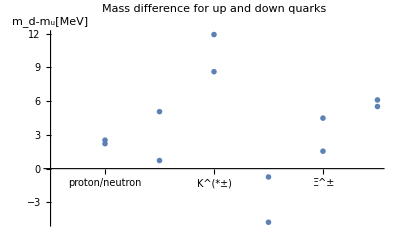

key | alpha | mass | q | a-S | S
proton | 0.94 | 938.272 | 2/9 | {-1.17,-0.65} | 1/2
neutron | 0.94 | 939.565 | -1/9 | {-1.17,-0.65} | 1/2
ρp | 0.86 | 775.96 | 2/9 | {-0.5,-0.1} | 1
ρn | 0.86 | 775.26 | -5/18 | {-0.5,-0.1} | 1
Ksp | 0.96 | 889.11 | 2/9 | {-0.1,-0.06} | 1
Ksn | 0.96 | 895.81 | -1/9 | {-0.1,-0.06} | 1
Σp | 0.95 | 1189.3 | 2/9 | {-0.193513,-0.128062} | 1/2
Σn | 0.95 | 1192.6 | -1/9 | {-0.193513,-0.128062} | 1/2
Ξn | 0.94 | 1314.86 | -1/9 | {-0.184,-0.035} | 1/2
Ξm | 0.94 | 1321.71 | 2/9 | {-0.184,-0.035} | 1/2
Dn | 0.86 | 1864.84 | -4/9 | {-0.14,0} | 1
Dp | 0.86 | 1869.61 | 2/9 | {-0.14,0} | 1

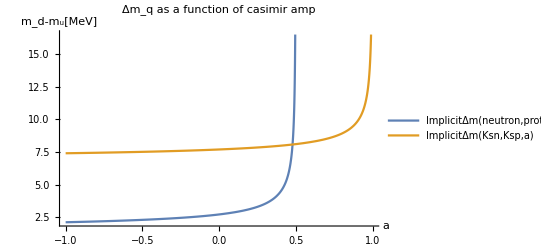

```mathematica
(*Generate Graph of Mass Differences*)
ListPlot[{
{1,ImplicitΔm[neutron,proton,-0.67]+0.000021},{1,ImplicitΔm[neutron,proton,-0.15]-0.000021},
{2,ImplicitΔm[ρn,ρp,0.5]-0.8},{2,ImplicitΔm[ρn,ρp,0.9]+0.8},
{3,ImplicitΔm[Ksn,Ksp,0.9]-1.2},{3,ImplicitΔm[Ksn,Ksp,0.94]+1.2},
{4,ImplicitΔm[Dp,Dn,0.86]+0.1},{4,ImplicitΔm[Dp,Dn,0.95]-0.1},
{5,ImplicitΔm[Ξm,Ξn,0.316]-0.024},{5,ImplicitΔm[Ξm,Ξn,0.465]+0.024},{6,ImplicitΔm[Σn,Σp,0.306487]-0.035},{6,ImplicitΔm[Σn,Σp,0.371938]+0.035},{7,ImplicitΔm[Kn,Kp,0.75]-0.02},{7,ImplicitΔm[Kn,Kp,0.99]+0.02},{8,ImplicitΔm[Bn,Bp,-0.00001]},{8,ImplicitΔm[Bn,Bp,-10^-8]}},PlotMarkers->{"-",30},AxesLabel->{"","m_d-m_u[MeV]"},
PlotLabel->"Mass difference for up and down quarks",Ticks->{{{1,"proton/neutron"},{2,"ρ^±"},{3,"K^(*±)"},{4,"D^±"},{5,"Ξ^±"},{6,"Σ^±"},{7,"K^±"}}, Automatic}]

(*Generate Data Table*)
Grid[Prepend[Table[{keys[[i]],α[keys[[i]]],Mass[keys[[i]]],Q[keys[[i]]],intercepts[keys[[i]]]-Spin[keys[[i]]],Spin[keys[[i]]]},{i,Length[keys]}],{key,alpha,mass,q,a-S,S}],Frame->All]
(*Generate Graph of Proton-Neutron vs K^* mass differences*)
Plot[{ImplicitΔm[neutron,proton,a],ImplicitΔm[Ksn,Ksp,a]},{a,-1,1},PlotLabel->"Δm_q as a function of casimir amp",PlotLegends->"Expressions",AxesLabel->{"a","m_d-m_u[MeV]"}]
```

#### Light quarks

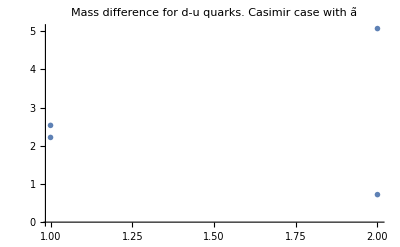

```mathematica
ListPlot[{
{1,ImplicitΔm[neutron,proton,-0.67]+0.000021},{1,ImplicitΔm[neutron,proton,-0.15]-0.000021},
{2,ImplicitΔm[ρn,ρp,0.5]-0.8},{2,ImplicitΔm[ρn,ρp,0.9]+0.8}}
,PlotMarkers->{"-",30},
PlotLabel->"Mass difference for d-u quarks. Casimir case with ã"]
```

#### Strange hadrons

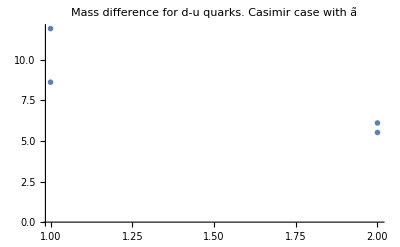

```mathematica
ListPlot[{
{1,ImplicitΔm[Ksn,Ksp,0.9]-1.2},{1,ImplicitΔm[Ksn,Ksp,0.94]+1.2},
{2,ImplicitΔm[Σn,Σp,0.306487]-0.035},{2,ImplicitΔm[Σn,Σp,0.371938]+0.035}},PlotMarkers->{"-",30},
PlotLabel->"Mass difference for d-u quarks. Casimir case with ã"]
```

#### Charm hadrons

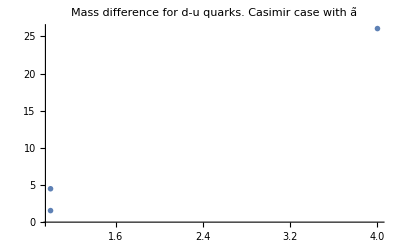

```mathematica
ListPlot[{
{1,ImplicitΔm[Ξm,Ξn,0.316]-0.024},{1,ImplicitΔm[Ξm,Ξn,0.465]+0.024},{4,ImplicitΔm[Dp,Dn,0.86]-0.1},{4,ImplicitΔm[Dp,Dn,1]+0.1}},PlotMarkers->{"-",30},
PlotLabel->"Mass difference for d-u quarks. Casimir case with ã"]
```

#### Misc

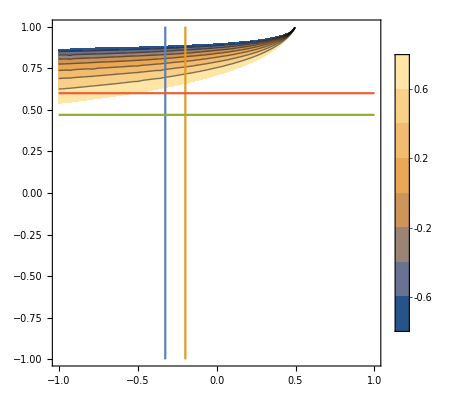

```mathematica
mpl=ContourPlot[ImplicitΔm[neutron,proton,Subscript[a, p]]-ImplicitΔm[ρn,ρp,Subscript[a, ρ]],{Subscript[a, p],-1,1},{Subscript[a, ρ],-1,1},PlotLegends->Automatic,PlotRange->{-0.8,0.8}];
fpl=ContourPlot[{Subscript[a, p]== -0.32498448657770906,Subscript[a, p]==-0.19779200441658287 ,Subscript[a, ρ] == 0.46978229750300965,Subscript[a, ρ] == 0.6},{Subscript[a, p],-1,1},{Subscript[a, ρ],-1,1}];
Show[mpl,fpl]
```

There is a match in mass differences for (a_ρ,a_p)≃(0.58,-0.3). The resulting mass difference is

```mathematica
ImplicitΔm[neutron,proton,-0.3]
```

2.18628

### commands

plot the possible values of m_d-m_u for different hadrons (varying the intercept). Is there a possible intersection for all of them? If so how constrained?

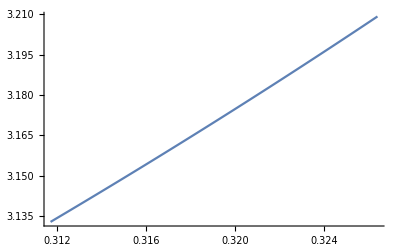

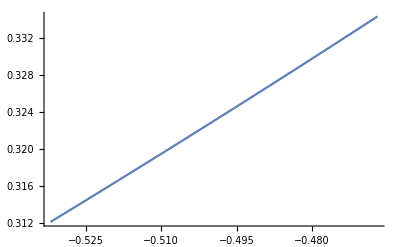

```mathematica
ppl=Plot[ImplicitΔm[neutron,proton,a],{a,0.3264,0.3117},RegionFunction->ImplicitΔm[neutron,proton,a]∈Reals] 
ρpl=Plot[ImplicitΔm[ρn,ρp,a],{a,-0.532,-0.467},RegionFunction->ImplicitΔm[ρn,ρp,a]∈Reals]
```

```mathematica
ΞDif=ListPlot[{ImplicitΔm[Ξn,Ξm,-0.53,ImplicitΔm[Ξn,Ξm,0.499]]},Filling->ImplicitΔm[Ξn,Ξm,-0.53],PlotMarkers-> {"-",20}]
(*{amin,amax}=InterceptLimits[ρn,α[ρn] 10^-6]
ρDif=ListPlot[{ImplicitΔm[ρn,ρp,amin,ImplicitΔm[ρn,ρp,amax]]},Filling->ImplicitΔm[ρn,ρp,amin],PlotMarkers-> {"-",20}];
{amin,amax}=InterceptLimits[Ksn,α[Ksn] 10^-6]
KsDif=ListPlot[{ImplicitΔm[Ksn,Ksp,amin,ImplicitΔm[Ksn,Ksp,amax]]},Filling->ImplicitΔm[Ksn,Ksp,amin],PlotMarkers-> {"-",20}];
Show[ΞDif,ρDif,KsDif]*)
```

-Graphics-

Now plot the energy differences due to charge and string tension, minus the difference in the actual experimental mass. This should give the mass difference in the end points needed to explain the mass difference.

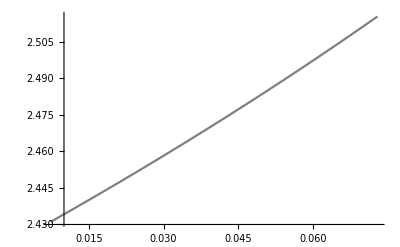

```mathematica
Nbaryon=Plot[Mass[neutron]-Mass[proton]-M[neutron,csq]+M[proton,csq],{csq,1/137,10/137},PlotStyle->Gray];
Ks=Plot[Mass[Ksn]-Mass[Ksp]-M[Ksn,csq]+M[Ksp,csq],{csq,0.5/137,10/137},PlotStyle->Red];
Ξc=Plot[Mass[Ξcn]-Mass[Ξcp]-M[Ξcn,csq]+M[Ξcp,csq],{csq,0.5/137,10/137},PlotStyle->Blue];
Dmes=Plot[Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,0.5/137,10/137},PlotStyle->Green];
(*Σc=Plot[Mass[Σcn]-Mass[Σcp]-M[Σcn,csq]+M[Σcp,csq],{csq,0.5/137,10/137},PlotStyle->Yellow];*)
Σ=Plot[Mass[Σn]-Mass[Σp]-M[Σn,csq]+M[Σp,csq],{csq,0.5/137,10/137},PlotStyle->Purple];
Ξ2=Plot[Mass[Ξ2m]-Mass[Ξ2n]-M[Ξ2m,csq]+M[Ξ2n,csq],{csq,0.5/137,10/137},PlotStyle->Dashed];
ρ=Plot[Mass[ρn]-Mass[ρp]-M[ρn,csq]+M[ρp,csq],{csq,0.5/137,10/137},PlotStyle->{Dashed,Red}];
B=Plot[Mass[Bn]-Mass[Bp]-M[Bn,csq]+M[Bp,csq],{csq,0.5/137,10/137},PlotStyle->{Dashed,Blue}];
Show[Nbaryon,Ks,Ξc,Dmes,(*Σc,*)Σ,ρ,Ξ2,B]
```

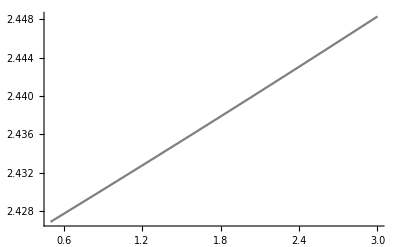

```mathematica
Nbaryon=Plot[Mass[neutron]-Mass[proton]-M[neutron,csq/137]+M[proton,csq/137],{csq,0.5,3},PlotStyle->Gray];
ρ=Plot[Mass[ρn]-Mass[ρp]-M[ρn,csq/137]+M[ρp,csq/137],{csq,0.5,3},PlotStyle->{Dashed,Red}];
Show[Nbaryon,ρ]
```

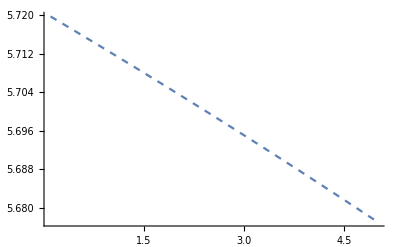

```mathematica
(*Ks=Plot[Mass[Ksn]-Mass[Ksp]-M[Ksn,csq/137]+M[Ksp,csq/137],{csq,0.1,1},PlotStyle->Red];*)
Ξ=Plot[Mass[Ξm]-Mass[Ξn]-M[Ξm,csq/137]+M[Ξn,csq/137],{csq,0.1,5},PlotStyle->Dashed]
(*Show[Ks,Ξ]*)
```

```mathematica
Mass[neutron]-Mass[proton]-M[neutron,3/137]+M[proton,3/137]
```

2.44829

```mathematica
Mass[ρn]-Mass[ρp]-M[ρn,1/137]+M[ρp,1/137]
```

0.557388

```mathematica
Mass[Ξm]-Mass[Ξn]-M[Ξm,2.8/137]+M[Ξn,2.8/137]
```

5.6968

```mathematica
Mass[Ksn]-Mass[Ksp]-M[Ksn,1/137]+M[Ksp,1/137]
```

7.49324

```mathematica
N[1/137]
```

0.00729927

There is an intersection
For the N baryon the mass difference is md-mu
For the K^* the mass difference is md-mu
For the Ξ_c the mass difference is md-mu
For the D the mass difference is md-mu
For the Σ_c the mass difference is md-mu
For the Σ the mass difference is md-mu
We can thus get very good agreement on the mass difference (The K^* should get a seperate treatment. Also this could be due to peculiarities in the mass of the K^*...) of d and u quarks.

```mathematica
FindRoot[Mass[neutron]-Mass[proton]-M[neutron,csq]+M[proton,csq]==Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,1/137}]
(Mass[neutron]-Mass[proton]-M[neutron,csq]+M[proton,csq]) /.FindRoot[Mass[Ξcn]-Mass[Ξcp]-M[Ξcn,csq]+M[Ξcp,csq]==Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,1/137}]
```

{csq→-0.285756}

1.29333-822.955 √(-1/1233-1/2 (-1/2+csq) π)+822.955 √(2/1233-1/2 (-1/2+csq) π)/.FindRoot[Mass[Ξcn]-Mass[Ξcp]-M[Ξcn,csq]+M[Ξcp,csq]==Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,1/137}]

This Gives a charge squared of about

```mathematica
N[6.5/137]
```

0.0474453

We can now fix the charge squared to this value and calculate the masses of the up and down quarks from the equations for the proton and neutron

```mathematica
CSQ=csq/.FindRoot[Mass[neutron]-Mass[proton]-M[neutron,csq]+M[proton,csq]==Mass[Dn]-Mass[Dp]-M[Dn,csq]+M[Dp,csq],{csq,1/137}];
mdmuSol=NSolve[{TotM[neutron,CSQ]== Mass[neutron],TotM[proton,CSQ]== Mass[proton]},{md,mu}]
```

{{md→12.7923,mu→10.5979}}

A consistency check is the mass of the pion, which turns out as

```mathematica
TotM[πp,CSQ]
Mass[πp]
```

577.473+md+mu

139.57

which is inconsistent. This tells us our model is not fit to determine the π mass as is.
Knowing these masses now enables us to determine the mass of the charm quark through the Ξ_c,Σ_c baryons and D Meson, and also consistency checks at the same time (the system of equations is over determined)

```mathematica
NSolve[TotM[Ξcn,CSQ]== Mass[Ξcn],{mc}]/.mdmuSol
NSolve[TotM[Ξcp,CSQ]== Mass[Ξcp],{mc}]/.mdmuSol
```

{{{mc→2458.09-(398.942 (1.23426+0.00729927 Missing[KeyAbsent,Ξcn]))/(√((1.23426+0.00729927 Missing[KeyAbsent,Ξcn]) Missing[KeyAbsent,Ξcn]))-(398.942 √((1.23426+0.00729927 Missing[KeyAbsent,Ξcn]) Missing[KeyAbsent,Ξcn]))/Missing[KeyAbsent,Ξcn]}}}

{{{mc→2457.2-(398.942 (1.23426+0.00729927 Missing[KeyAbsent,Ξcp]))/(√((1.23426+0.00729927 Missing[KeyAbsent,Ξcp]) Missing[KeyAbsent,Ξcp]))-(398.942 √((1.23426+0.00729927 Missing[KeyAbsent,Ξcp]) Missing[KeyAbsent,Ξcp]))/Missing[KeyAbsent,Ξcp]}}}

```mathematica
NSolve[TotM[Dn,CSQ]== Mass[Dn],{mc}]/.mdmuSol
NSolve[TotM[Dp,CSQ]== Mass[Dp],{mc}]/.mdmuSol
```

{{{mc→632.496}}}

{{{mc→660.598}}}

```mathematica
NSolve[TotM[Σcn,CSQ]== Mass[Σcn],{mc}]/.mdmuSol
NSolve[TotM[Σcp,CSQ]== Mass[Σcp],{mc}]/.mdmuSol
```

{{{mc→1531.79}}}

{{{mc→1532.25}}}

We can now use the Σ baryons as a probe into the strange quark.

```mathematica
NSolve[TotM[Σn,CSQ]== Mass[Σn],{ms}]/.mdmuSol
NSolve[TotM[Σp,CSQ]== Mass[Σp],{ms}]/.mdmuSol
```

{{{ms→270.65}}}

{{{ms→268.648}}}

```mathematica
Factor[Δmsq[ρn,πn,0.5,0]]/10^6  /. {md-> 0,mu->0}
Factor[Δmsq[ρn,πn,0.9,0]]/10^6 /. {md-> 0,mu->0}
```

0.581395+0. ⅈ

0.116279-1.73472×10^-18 ⅈ

```mathematica
(776.6944326034911^2-636.168^2)/10^6
```

0.198545

```mathematica
{6,ImplicitΔm[Bn,Bp,-0.01]-0.16}
```

{6,8.41153}

# Mass Differences predictions for J=1

## Data

```mathematica
mu=150;
md=152.1;
ms=601;
mc=0;
keys={proton,neutron,ρp,ρn,Σp,Σn,Ξn,Ξm};
dm1=<| proton ->mu ,neutron-> md,Ξcn-> mc,Ξcp-> mc,Σcp->mc,Σcn->mc,Σp->ms,Σn->ms ,ρn->(mu+md)/2,ρp->mu,Bn-> mb,Bp-> mb, Ξn-> ms,Ξm->ms,Kn->ms,Kp-> ms|>;
dm2=<| proton -> md,neutron-> md,Ξcn-> md,Ξcp-> mu,Σcp->mu,Σcn->md,Σp->mu,Σn->md,ρn->(mu+md)/2,ρp->md, Ξn->ms,Ξm->ms |>;
dSpin=<| proton ->1/2,neutron ->1/2 ,Ξcn-> 1/2,Ξcp-> 1/2,Σcp->1/2,Σcn->1/2,Σp->1/2,Σn->1/2,ρn->1,ρp->1, Ξn->1/2,Ξm-> 1/2|>;
dq1=<| proton -> 1/3,neutron-> 1/3,Σcp->0,Σcn->0,Σp->1/3,Σn->1/3,ρn->1/2,ρp->2/3 , Ξn->0,Ξm->0|>;
dq2=<| proton -> 2/3,neutron-> -1/3,Σcp->0,Σcn->0,Σp->2/3,Σn->-1/3,ρn->-1/2,ρp->1/3 , Ξn->0,Ξm->0|>;
dα=<| proton->0.94 10^-6,neutron-> 0.94 10^-6,Σcn->0.95 10^-6,Σcp->0.95 10^-6,Σn->0.95 10^-6,Σp->0.95 10^-6 ,ρn->0.86 10^-6,ρp->0.86 10^-6, Ξn->.94 10^-6,Ξm-> 0.94 10^-6|>;
(*for summup purposes*)
intercepts=<| proton ->-0.41,neutron-> -0.41 ,Σp->0.339213,Σn->0.339213,ρn->0.86,ρp->0.86, Ξn->0.3905,Ξm->0.3905  |>;
```

## Definitions

```mathematica
Bisect[xmin_,xmax_,f_,accur_:10^-5]:=Module[{x1=N[xmin],x2=N[xmax],xmid=N[(xmin+xmax)/2],step=0},(*Print[{step,Maxsteps,Abs[f[xmid]]>accur}]*)

 While[Abs[f[xmid]]>accur,
If[Sign[Re[f[x1]f[xmid]]]>0,
x1=xmid,
x2=xmid];
xmid=N[(x1+x2)/2];
Sign[f[x1]f[xmid]]];
xmid];

eqΔθ[β1_,m1_,m2_,Δθ_]:=Δθ^2-β1^2-β2^2-2 β1 β2 Cos[Δθ]/.Solve[β1 m1 β2^2+β2 m2 (1-β1^2)-β1 m1==0,β2][[2,1]];

Δθmax=Evaluate[Δθ /. FindRoot[1-Δθ/(2*Cos[Δθ/2]),{Δθ,1.2}]];

Feq[β1_,m1_,m2_,q1_,q2_,T_,ω_,a_,Spin_]:=T √(1-β1^2)-(m1 β1 ω)/(√(1-β1^2))-1/137 q1 q2 ω^2 (β1+2 β1 β2^2+β1^3 β2^2+β2 (1+β1^2 (2+β2^2)) Cos[Δθ]+(1+β1^2) β2 Δθ Sin[Δθ])/(Δθ+β1 β2 Sin[Δθ])^3+π/2((a-Spin) ω^2)/(β1+β2)^2/.{Solve[β1 m1 β2^2+β2 m2 (1-β1^2)-β1 m1==0,β2][[2,1]],FindRoot[eqΔθ[β1,m1,m2,Δθ],{Δθ,Δθmax}][[1]]};

ModelDynamics[β1_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,a_?NumericQ,Spin_?NumericQ]:=Module[{β2,ω,Δθ,T=1/(2π α)},
Δθ=Δθ/.FindRoot[eqΔθ[β1,m1,m2,Δθ],{Δθ,Δθmax}][[1]];
β2=β2/.Solve[β1 m1 β2^2+β2 m2 (1-β1^2)-β1 m1==0,β2][[2,1]];
ω=ω/.Solve[Feq[β1,m1,m2,q1,q2,T,ω,a,Spin]==0&&ω≥0,ω,Reals][[1]](*change to [[1]]*);
{β2,ω,Δθ}];
(*check goodness of solution for eom*)
CheckSol[β1_,m1_,m2_,α_,q1_,q2_,a_,Spin_]:=Module[{β2,Δθ,ω,T=1/(2π α)},
{β2,ω,Δθ}=ModelDynamics[β1,m1,m2,α,q1,q2,a,Spin];

{Feq[β1,m1,m2,q1,q2,T,ω,a,Spin],eqΔθ[β1,m1,m2,Δθ]}];

EMContribution[β1_,m1_,m2_,α_,q1_,q2_,a_,Spin_]:=Module[{β2,Δθ,ω,T=1/(2π α),EM,Casimir,Tension,Centrifugal},
{β2,ω,Δθ}=ModelDynamics[β1,m1,m2,α,q1,q2,a,Spin];
EM=Abs[1/137 q1 q2 ω^2 (β1+2 β1 β2^2+β1^3 β2^2+β2 (1+β1^2 (2+β2^2)) Cos[Δθ]+(1+β1^2) β2 Δθ Sin[Δθ])/(Δθ+β1 β2 Sin[Δθ])^3];
Casimir=Abs[π/2((a-Spin) ω^2)/(β1+β2)^2];
Tension=Abs[T √(1-β1^2)];
Centrifugal=Abs[(m1 β1 ω)/(√(1-β1^2))];
{EM/Centrifugal,EM/Casimir,EM/Tension}];

energy[β1_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,a_?NumericQ,Spin_?NumericQ]:=Module[{β2,γ1,γ2,L,ω,Δθ,T=1/(2π α)},
{β2,ω,Δθ}=ModelDynamics[β1,m1,m2,α,q1,q2,a,Spin]; 
γ1=1/(√(1-β1^2));
γ2=1/(√(1-β2^2));
T/ω(ArcSin[β1]+ArcSin[β2])+(m1 γ1+m2 γ2)+1/137 q1 q2 ω (1/(β1 β2 Sin[Δθ]+Δθ))-π/2((a-Spin) ω)/(β1+β2)];

j[β1_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,a_?NumericQ,Spin_?NumericQ]:=Module[{β2,γ1,γ2,ω,Δθ,T=1/(2π α)},
If[β1==0,0,
γ1=1/Sqrt[1-β1^2];
γ2=1/Sqrt[1-β2^2];
{β2,ω,Δθ}=ModelDynamics[β1,m1,m2,α,q1,q2,a,Spin];
T(-β1/γ1+ArcSin[β1]-β2/γ2+ArcSin[β2])/(2 ω^2)+m1(γ1 β1^2)/ω+m2(γ2 β2^2)/ω-2/137 q1 q2 β1 β2 Cos[Δθ]/(β1 β2 Sin[Δθ]+Δθ)]];

βJ[J_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,a_,Spin_,accur_:10^-10]:=
Module[{β,βmin,βmax,jJ},
βmin=0;βmax=1-10^-15;
jJ=(j[#,m1,m2,α,q1,q2,a,Spin]-J)&;
β=Bisect[βmin,βmax,jJ,accur]];

EJ[J_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,a_?NumericQ,Spin_?NumericQ]:=
Module[{β1},
β1=βJ[J,m1,m2,α,q1,q2,a,Spin];
energy[β1,m1,m2,α,q1,q2,a,Spin]];

JStringLength[J_?NumericQ,m1_?NumericQ,m2_?NumericQ,α_?NumericQ,q1_?NumericQ,q2_?NumericQ,a_?NumericQ,Spin_?NumericQ]:=
Module[{β1},
β1=βJ[J,m1,m2,α,q1,q2,a,Spin];(β1+ModelDynamics[β1,m1,m2,α,q1,q2,a,Spin][[1]])/ModelDynamics[β1,m1,m2,α,q1,q2,a,Spin][[2]]];

PredictMassDiff[key1_,key2_,J_]:= EJ[J,dm1[key1],dm2[key1],dα[key1],dq1[key1],dq2[key1],intercepts[key1],dSpin[key1]]-EJ[J,dm1[key2],dm2[key2],dα[key2],dq1[key2],dq2[key2],intercepts[key2],dSpin[key2]];

GetStringLength[key1_,J_]:= JStringLength[J,dm1[key1],dm2[key1],dα[key1],dq1[key1],dq2[key1],intercepts[key1],dSpin[key1]];
```

## Calculation

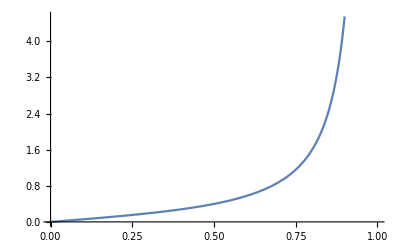

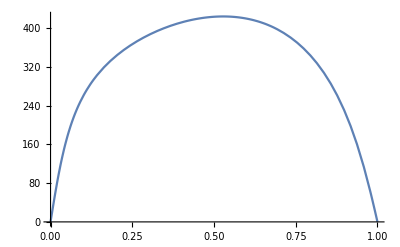

```mathematica
Plot[j[x,120,120,0.9 10^-6,1/3,2/3,0.1,1],{x,0,1}]
Plot[ModelDynamics[x,120,11,0.9 10^-6,1/3,2/3,0.1,1][[2]],{x,0,1}]
```

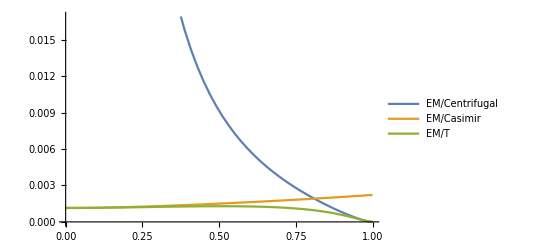

```mathematica
Plot[{EMContribution[x,120,111,0.9 10^-6,1/3,2/3,0.1,1][[1]],EMContribution[x,120,111,0.9 10^-6,1/3,2/3,0.1,1][[2]],EMContribution[x,120,111,0.9 10^-6,1/3,2/3,0.1,1][[3]]},{x,0,1},PlotLegends-> {"EM/Centrifugal","EM/Casimir","EM/T"}]
```

```mathematica
PredictMassDiff[neutron,proton,1]
```

0.851626

```mathematica
PredictMassDiff[neutron,proton,2]
```

0.769377

```mathematica
PredictMassDiff[Σn,Σp,1]
```

0.372603

```mathematica
PredictMassDiff[Σn,Σp,3]
```

0.508185

```mathematica
(GetStringLength[neutron,1]-GetStringLength[proton,1])/GetStringLength[neutron,1]
```

-0.00180204

# Decay Rates

Decay rates are calculated as Γ=Le^(-m_q/T). m_q is the mass of each of the quarks created in the decay. T is the tension.

## Data

```mathematica
(*The mass of the Ksp is the hadroproduced one*)
Mass=<| proton -> 938.27204,neutron-> 939.56537,Ksp->889.11,Ksn->  895.81, Ξcn-> 2470.88,Ξcp-> 2467.8,Λcp->2286.46,Dn-> 1864.84 ,Dp-> 1896.61  ,πp-> 139.57,πn-> 134.97,Σcp->2452.9,Σcn->2453.74,Σp->1189.3,Σn->1192.6 ,ρn->775.26,ρp->775.96,Bn-> 5279.61,Bp-> 5279.29 , Ξn-> 1314.86,Ξm->1321.71,Kn->497.614,Kp-> 493.677|>;
m1=<| proton ->mu ,neutron-> md, Ksp-> ms, Ksn-> ms,Ξcn-> mc,Ξcp-> mc,Λcp->md,Dp->md,Dn->mu,πp-> mu,πn-> (mu+md)/2,Σcp->mc,Σcn->mc,Σp->ms,Σn->ms ,ρn->(mu+md)/2,ρp->mu,Bn-> mb,Bp-> mb, Ξn-> ms,Ξm->ms,Kn->ms,Kp-> ms|>;
m2=<| proton -> md,neutron-> md,Ksp-> mu, Ksn-> md,Ξcn-> md,Ξcp-> mu,Λcp->mc,Dp->mc,Dn->mc,πp-> md,πn-> (mu+md)/2,Σcp->mu,Σcn->md,Σp->mu,Σn->md,ρn->(mu+md)/2,ρp->md,Bn-> md,Bp-> mu, Ξn->ms,Ξm->ms,Kn->md,Kp-> mu |>;
Spin=<|Ksp-> 1,Ksn-> 1, proton ->1/2,neutron ->1/2 ,Ξcn-> 1/2,Ξcp-> 1/2,Λcp->1/2,Dn-> 1,Dp-> 1,πp->0,πn->0,Σcp->1/2,Σcn->1/2,Σp->1/2,Σn->1/2,ρn->1,ρp->1,Bn-> 0,Bp-> 0, Ξn->1/2,Ξm-> 1/2,Kn->0,Kp-> 0|>;
Q=<|Ksp->2/9,Ksn->-1/9 , proton -> 2/9,neutron-> -1/9,Λcp->2/9,Dn-> -4/9,Dp-> 2/9,πp->2/9,πn->-5/18,Σcp->2/9,Σcn->-1/9,Σp->2/9,Σn->-1/9,ρn->-5/18,ρp->2/9,Bn-> -1/9,Bp->2/9 , Ξn->-1/9,Ξm-> 2/9,Kn->-1/9,Kp-> 2/9|>;
α=<|Ksp->0.96,Ksn->0.96, proton->0.94,neutron-> 0.94,Λcp->0.95,Dp->0.86,Dn->0.86,πp->0.86,πn->0.86 ,Σcn->0.95,Σcp->0.95,Σn->0.95,Σp->0.95 ,ρn->0.86,ρp->0.86,Bn-> 0.86,Bp-> 0.86, Ξn->.94,Ξm-> .94,Kn->0.86,Kp-> 0.86|>;
```